# ARC barrel RICH

Geometry and Optica ray tracing of the ARC barrel RICH, from ARCGeometryData.wl (numbers extracted from the ARC XML and C++ constructor), ARCBarrel.wl (pure Mathematica geometry, no Optica) and ARCBarrelOptica.wl (Optica adapter, here adapted to OpticaEM). The three files are in the project folder src/ (moved there on 2026-11-13): ARCBarrel.wl is loaded by the project loader (LoadRICHCase["arc"], src/LoadProject.wl). Global frame {Z beam, X, Y}: the first axis is the beam axis, as in the LHCb optics (changed on 2026-11-13; it was {X, Y, Z beam}). Units: mm, rad; Optica wavelengths in micrometres. The same geometry is the detector "ARC barrel" of optics.nb (detector list src/detectors.wl), whose source chr is the cone of Test 1. Use a fresh kernel (Evaluation > Quit Kernel) if optics.nb was evaluated in the same kernel: the adapter adds its own refractive-index models to ModelRefractiveIndex.

## Geometry (no Optica)

```mathematica
(*FIX 2026-11-13: the ARC files are in src/; ARCBarrel.wl is loaded by the project loader (case "arc" of src/LoadProject.wl)*)
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"src","LoadProject.wl"}]];
LoadRICHCase["arc"];
```

```mathematica
b1 = ARCBarrel["Row" -> 1, "Phi" -> 0];(* "Row" -> 2 or "Both"; "Phi" -> Automatic keeps the orientation of the source files *)
Length[b1["Cells"]](* 17 cells; row 2: 16; both: 33 *)
```

17

```mathematica
ARCBarrelTable[b1](* cell positions, eta, mirror radii and centres, sensor tilts, global mm *)
```

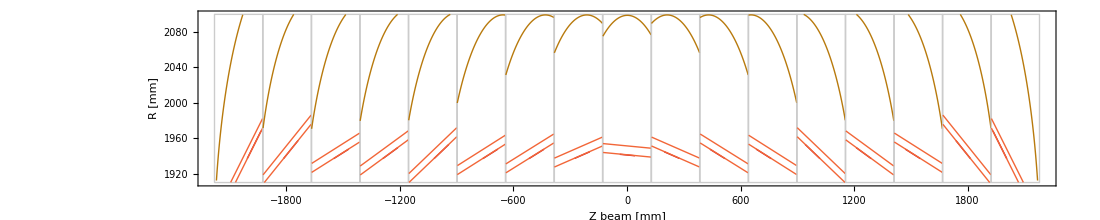

```mathematica
ARCBarrelSection[b1](* Z-R section of one row: mirrors (brown), sensors (red), aerogel plates (orange) *)
```

```mathematica
ARCBarrelGraphics[b1](* 3D view, a few seconds *)
```

-Graphics3D-

```mathematica
{ARCIndex["Gas", 400.], ARCIndex["Aerogel", 400.]}(* refractive indices at 400 nm: 1.0013268, 1.0309500 *)
```

{1.00133,1.03095}

## Ray tracing with Optica (OpticaEM)

Loads OpticaEM if not loaded yet. Run the two self-checks first: both must succeed before tracing (the adapter installs its own intersection functions on the Optica surfaces).

```mathematica
(*FIX 2026-11-13: the ARC files are in src/*)
Get[RICHProjectPath["src","ARCBarrelOptica.wl"]];
```

Begin loading Optica EM ...

Note that EM functions will be compiled with the setting: $EMCompilationTarget = "WVM"

```mathematica
ARCOpticaClipSelfCheck[](* must be True *)
```

True

```mathematica
ARCOpticaMediaSelfCheck[](* GasAccepted and AerogelAccepted must be True; indices at 400 nm about 1.0013 and 1.031 *)
```

<|GasAccepted→True,AerogelAccepted→True,GasIndex400nm→1.00133,AerogelIndex400nm→1.03095|>

Validation (2026-11-08). The tests below trace Cherenkov photons with Optica, one cell at a time, and compare the result with an independent geometric model written in plain Mathematica (reflection on the spherical mirror, intersection with the sensor plane, no aerogel). The adapter needed one fix for OpticaEM: Rotate[object, matrix] applies the transpose of the matrix (see place[] in ARCBarrelOptica.wl). Before that fix the mirrors were mirrored about the cell axis and the aerogel and sensor planes were tilted (0.029 rad in cell 1), so most photons missed the sensor window of the hit search.

### Tools for the tests

traceCell[n, rEm, λ, nPhot] traces with Optica, in cell n of row 1 only, a cone of nPhot Cherenkov photons (β = 1, wavelength λ in nm) emitted at the point at radius rEm (mm) on the cell axis, by a track coming from the interaction point. It returns the cell, the Cherenkov angle, the ray segments, the height of every segment end above the sensor front (along the sensor normal) and the photon hits on the sensor in sensor coordinates (e, v) in mm. geoCell[n, rEm, λ, nPhot] gives the same sensor hits from the geometric model. ringFit fits a circle (centre, radius, rms of the distances); maxDist is the largest distance between a model hit and the nearest Optica hit; surfaceOf says where the ray segments end.

```mathematica
pts[x_] := Cases[x, {_?NumericQ, _?NumericQ, _?NumericQ}, Infinity];
cellOf[n_] := SelectFirst[b1["Cells"], #["SignedNumber"] == n &];
traceCell[n_, rEm_ : 2000., lambda_ : 400., nPhot_ : 36] := Module[{cell = cellOf[n], p, th, rays, sysCell, traced, ends},
  p = ARCToGlobal[cell, {0., 0., rEm}];
  th = ArcCos[1/ARCIndex["Gas", lambda]];
  rays = ARCOpticaRays[p, ARCCherenkovCone[Normalize[p], th, nPhot], lambda, "Gas"];
  sysCell = ARCOpticaSystem[Append[b1, "Cells" -> {cell}], "FullBoundaryModel" -> False];
  traced = PropagateSystem[{rays, sysCell}];
  ends = pts@ReadRays[traced, RayEnd];
  <|"Cell" -> cell, "CherenkovAngle" -> th, "Traced" -> traced,
    "Segments" -> Transpose[{pts@ReadRays[traced, RayStart], ends}],
    "Heights" -> ((ARCToLocal[cell, #] - cell["SensorFront"]) . cell["PlaneN"] & /@ ends),
    "SensorHits" -> Cases[With[{d = ARCToLocal[cell, #] - cell["SensorFront"]}, {d . cell["PlaneE"], d . cell["PlaneV"], d . cell["PlaneN"]}] & /@ ends,
      {e_, v_, h_} /; Abs[h] < 0.01 && Abs[e] <= cell["SensorHalfSizes"][[1]] && Abs[v] <= cell["SensorHalfSizes"][[2]] :> {e, v}]|>];
geoCell[n_, rEm_ : 2000., lambda_ : 400., nPhot_ : 36] := Module[{cell = cellOf[n], pL, th, mc, rad, sf},
  pL = {0., 0., rEm}; th = ArcCos[1/ARCIndex["Gas", lambda]];
  mc = cell["MirrorCentre"]; rad = cell["MirrorInnerRadius"]; sf = cell["SensorFront"];
  Map[Function[d, Module[{q = pL - mc, b, m, nrm, r, h},
      b = q . d; m = pL + (-b + Sqrt[b^2 - (q . q - rad^2)]) d;
      nrm = Normalize[m - mc]; r = d - 2 (d . nrm) nrm;
      h = m + ((sf - m) . cell["PlaneN"])/(r . cell["PlaneN"]) r;
      {(h - sf) . cell["PlaneE"], (h - sf) . cell["PlaneV"]}]],
   Transpose[cell["Rotation"]] . # & /@ ARCCherenkovCone[Normalize[ARCToGlobal[cell, pL]], th, nPhot]]];
ringFit[h_List] := If[Length[h] < 3, <|"Centre" -> Missing[], "Radius" -> Missing[], "RMS" -> Missing[]|>,
  Module[{c0 = Mean[h], r}, r = Norm[# - c0] & /@ h; <|"Centre" -> c0, "Radius" -> Mean[r], "RMS" -> StandardDeviation[r]|>]];
maxDist[model_List, optica_List] := If[optica === {}, Missing[], Max[Function[g, Min[Norm[g - #] & /@ optica]] /@ model]];
surfaceOf[t_] := Module[{cell = t["Cell"], hA, hW},
  hA = (cell["AerogelCentre"] - cell["SensorFront"]) . cell["PlaneN"]; hW = cell["AerogelHalfThickness"];
  Counts[Which[Abs[#] < 0.01, "sensor front", Abs[# - (hA + hW)] < 0.01, "aerogel outer face", Abs[# - (hA - hW)] < 0.01, "aerogel inner face", # > 50, "mirror", True, "other"] & /@ t["Heights"]]];
```

### Test 1: central cell, 400 nm

Cell 1 of row 1 (z = 0). The track comes from the interaction point and crosses the cell along its axis; the 36 photons are emitted at R = 2000 mm, between the sensor (front at about 1941 mm) and the mirror (about 2098 mm), with the Cherenkov angle of C4F10 at 400 nm (51.5 mrad).

```mathematica
t1 = traceCell[1];
```

3D view: geometry of cell 1 (mirror in gold, sensor in red, cell walls in grey) and the 36 traced photons (blue): up to the mirror, then back down through the aerogel plate to the sensor.

```mathematica
Show[ARCBarrelGraphics[Append[b1, "Cells" -> {t1["Cell"]}], "Aerogel" -> False], Graphics3D[{Blue, Line /@ t1["Segments"]}], PlotRange -> All, ImageSize -> 500]
```

-Graphics3D-

Where the ray segments end. Expected: 36 on the mirror, 36 on each face of the aerogel plate, 36 on the sensor front (absorbed there): 144 ray/surface intersections. A wrong placement of the planes shows up here at once (before the fix the sensor heights spread over ±0.3 mm and few ends were found on the sensor front).

```mathematica
surfaceOf[t1]
```

<|mirror→36,aerogel outer face→36,aerogel inner face→36,sensor front→36|>

The Cherenkov ring on the sensor: Optica (blue, with refraction in the aerogel plate) and the geometric model (red, no aerogel). Expected from the model: radius 8.83 mm, centre (-0.35, 0) mm; Optica gave 8.82 mm on 2026-11-08 (the aerogel plate shifts the photons by a few micrometres). maxDist is the largest distance between a model hit and the nearest Optica hit.

```mathematica
g1 = geoCell[1];
<|"Optica" -> ringFit[t1["SensorHits"]], "model" -> ringFit[g1], "maxDist (mm)" -> maxDist[g1, t1["SensorHits"]]|>
```

<|Optica→<|Centre→{-0.361574,-5.92119×10^-16},Radius→8.82248,RMS→0.00293262|>,model→<|Centre→{-0.352545,-5.42776×10^-16},Radius→8.82935,RMS→0.00293999|>,maxDist (mm)→0.0159166|>

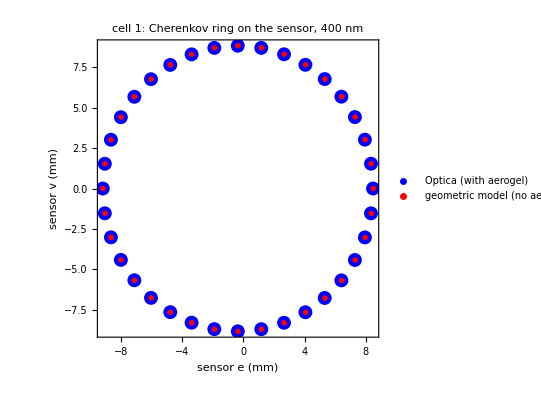

```mathematica
ListPlot[{t1["SensorHits"], g1}, PlotStyle -> {Directive[Blue, PointSize[0.025]], Directive[Red, PointSize[0.01]]},
 PlotLegends -> {"Optica (with aerogel)", "geometric model (no aerogel)"}, AspectRatio -> Automatic, Frame -> True,
 FrameLabel -> {"sensor e (mm)", "sensor v (mm)"}, PlotLabel -> "cell 1: Cherenkov ring on the sensor, 400 nm", ImageSize -> 400]
```

### Test 2: every cell of row 1

Same test for the 17 cells of row 1 (about a minute). Moving away from z = 0 the mirror centres move off the cell axis (up to 216 mm) and the sensors are tilted (up to 0.40 rad): this is where a wrong rotation or a wrong sign shows up. Expected: 36 photons on the sensor in every cell, Optica and model ring radii within a few hundredths of a millimetre (the aerogel plate is crossed at larger angles in the outer cells), maxDist small.

```mathematica
rowCells = #["SignedNumber"] & /@ b1["Cells"];
tests = AssociationMap[traceCell, rowCells];
geos = AssociationMap[geoCell, rowCells];
```

```mathematica
Dataset[Map[<|"cell" -> #, "Zcell (mm)" -> Round[tests[#]["Cell"]["CentreZ"], 0.1],
    "sensor tilt (rad)" -> Round[tests[#]["Cell"]["SensorTilt"], 0.0001],
    "photons on sensor" -> Length[tests[#]["SensorHits"]],
    "ring radius Optica (mm)" -> Round[ringFit[tests[#]["SensorHits"]]["Radius"], 0.001],
    "ring radius model (mm)" -> Round[ringFit[geos[#]]["Radius"], 0.001],
    "maxDist (mm)" -> Round[maxDist[geos[#], tests[#]["SensorHits"]], 0.001]|> &, rowCells]]
```

Rings on the sensors of five cells, from the most negative z to the most positive: the ring centre moves across the sensor while the radius stays about 8 mm.

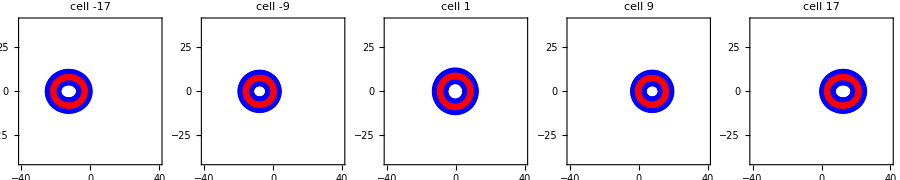

```mathematica
GraphicsRow[Table[ListPlot[{tests[n]["SensorHits"], geos[n]}, PlotStyle -> {Directive[Blue, PointSize[0.03]], Directive[Red, PointSize[0.012]]},
   AspectRatio -> Automatic, Frame -> True, PlotRange -> {{-40, 40}, {-40, 40}}, PlotLabel -> "cell " <> ToString[n]], {n, {-17, -9, 1, 9, 17}}], ImageSize -> 900]
```

### Test 3: chromatic dispersion of the gas radiator (cell 1)

The Cherenkov angle depends on the refractive index of C4F10, n(λ), so photons of different wavelength make rings of different radius on the sensor: this spread is the chromatic error of the radiator. Here cell 1 is traced at 250, 400 and 650 nm (ARCIndex interpolates the refractive-index table of the ARC XML).

```mathematica
lams = {250., 400., 650.};
chrom = AssociationMap[traceCell[1, 2000., #] &, lams];
Grid[Prepend[{Round[#], Round[ARCIndex["Gas", #], 0.000001], Round[1000 chrom[#]["CherenkovAngle"], 0.01],
     Round[ringFit[chrom[#]["SensorHits"]]["Radius"], 0.001], Round[ringFit[geoCell[1, 2000., #]]["Radius"], 0.001]} & /@ lams,
  {"wavelength (nm)", "n gas", "Cherenkov angle (mrad)", "ring radius Optica (mm)", "ring radius model (mm)"}], Frame -> All]
```

wavelength (nm) | n gas | Cherenkov angle (mrad) | ring radius Optica (mm) | ring radius model (mm)
250 | 1.0014 | 52.95 | 9.073 | 9.08
400 | 1.00133 | 51.48 | 8.822 | 8.829
650 | 1.0013 | 50.94 | 8.729 | 8.736

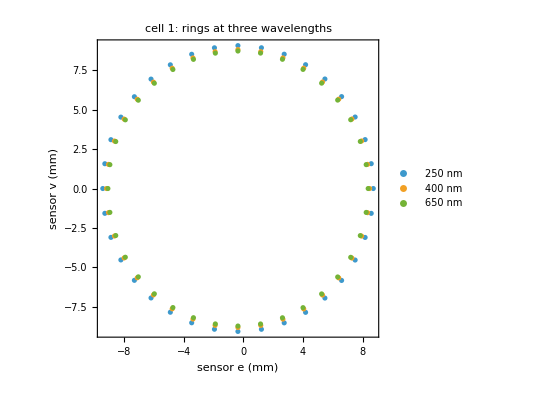

```mathematica
ListPlot[chrom[#]["SensorHits"] & /@ lams, PlotLegends -> (ToString[Round[#]] <> " nm" & /@ lams), AspectRatio -> Automatic,
 Frame -> True, FrameLabel -> {"sensor e (mm)", "sensor v (mm)"}, PlotLabel -> "cell 1: rings at three wavelengths", ImageSize -> 400]
```

### Test 4: gaps between sensor, aerogel and cooling plates (geometry, no Optica)

The ARC source sets a safe distance of 262 µm between the sensor and the aerogel plate and between the sensor and the cooling plate (safe_distance_from_sensor). In ARCBarrel.wl the aerogel and cooling centres are offset from the sensor centre along the radial axis of the cell, while the plates are oriented like the tilted sensor: the gaps are then 262 µm only where the sensor is not tilted, and in cells ±17 (tilt 0.40 rad) the aerogel plate overlaps the sensor by 0.24 mm. TO CHECK against ARC_barrel_geo.cpp: if the offsets are applied there in the sensor frame, ARCBarrel.wl should do the same.

```mathematica
Dataset[<|"cell" -> #["SignedNumber"], "sensor tilt (rad)" -> Round[#["SensorTilt"], 0.0001],
    "gap sensor-aerogel (mm)" -> Round[(#["AerogelCentre"] - #["SensorFront"]) . #["PlaneN"] - #["AerogelHalfThickness"], 0.001],
    "gap sensor-cooling (mm)" -> Round[(#["SensorFront"] - 2 #["SensorHalfSizes"][[3]] #["PlaneN"] - #["CoolingCentre"]) . #["PlaneN"] - #["CoolingHalfThickness"], 0.001]|> & /@ b1["Cells"]]
```

### Notes

Whole barrel: ARCOpticaSystem[b1] builds all 17 cells of a row, but DrawSystem of the whole barrel is not useful: Optica draws every flat face with its 1.2 m × 1.2 m search rectangle (it hides the rays) and the output is about 60 MB. Trace one cell at a time as above, and use ARCBarrelGraphics or ARCBarrelSection for the geometry. FullBoundaryModel -> False (used here) keeps the inner mirror surface, the aerogel and cooling faces and the sensor front; True adds all solid boundary faces.